# Notebook 10: Conditionals

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Conditional expressions

Most programming languages have a way of expressing statements of the form “IF some condition THEN do something OTHERWISE do something else.” These kind of expressions are known as conditionals. Mathematica has a number of them, including If and Which.

### If

The If command tests to see if a condition is True. If it is, it returns its second argument. If it is False, it returns its third argument.

```mathematica
If[True, Red,Blue]
```

RGBColor[1, 0, 0]

```mathematica
If[False,Red,Blue]
```

RGBColor[0, 0, 1]

There is an alternate version of If which returns a fourth argument if the condition is neither True nor False. The Undefined value is neither True nor False.

```mathematica
If[Undefined,Red,Blue,Green]
```

RGBColor[0, 1, 0]

### Which

The Which command lets us test as many conditions as we like. Each condition has a corresponding value. The value corresponding to the first condition to evaluate to True is returned.

```mathematica
Which[True,Red,True,Blue,True,Green,True,Orange]
```

RGBColor[1, 0, 0]

```mathematica
Which[False,Red,True,Blue,True,Green,True,Orange]
```

RGBColor[0, 0, 1]

```mathematica
Which[False,Red,False,Blue,True,Green,True,Orange]
```

RGBColor[0, 1, 0]

```mathematica
Which[False,Red,False,Blue,False,Green,True,Orange]
```

RGBColor[1, 0.5, 0]

## Animating a stop sign

Here is an example of how we might use a conditional statement. Let’s start by designing a stop sign. We will use darker, less opaque versions of each colour to represent lights that are off.

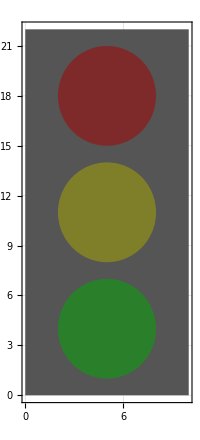

```mathematica
Graphics[{Darker[Gray],Rectangle[{0,0},{10,22}],Opacity[.5],Darker[Green],Disk[{5,4},3],Darker[Yellow],Disk[{5,11},3],Darker[Red],Disk[{5,18},3]},GridLines->Automatic,Frame->True]
```

Now we want to create a function that draws a stop light at a given position. We will also give our drawing function another parameter t that indicates time (in seconds). Then we will use a Which statement to use the time value to set the colour to green, amber or red.

```mathematica
drawStopLight[{x_,y_},t_]:=
{Darker[Gray],Rectangle[{x,y},{x+10,y+22}],Opacity[.5],Darker[Green],Disk[{x+5,y+4},3],Darker[Yellow],Disk[{x+5,y+11},3],Darker[Red],Disk[{x+5,y+18},3],Opacity[1],Which[t≤4,{Green,Disk[{x+5,y+4},3]},t≤6,{Yellow,Disk[{x+5,y+11},3]},t≤10,{Red,Disk[{x+5,y+18},3]}]}
```

Let’s test our three conditions

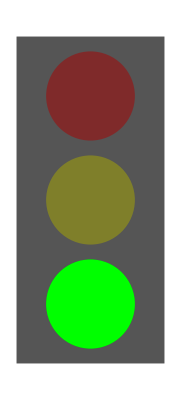
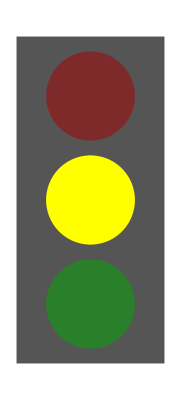
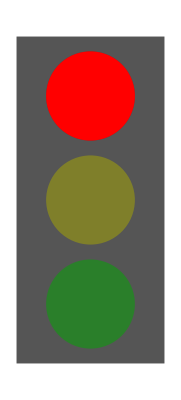

```mathematica
{Graphics[drawStopLight[{0,0},2]],Graphics[drawStopLight[{0,0},5]],Graphics[drawStopLight[{0,0},7]]}
```

Now we can use Table and ListAnimate to create an animation

```mathematica
stopSignFrames=Table[Graphics[{LightBlue,Rectangle[{0,0},{50,50}],Darker[Gray],Polygon[{{2,2},{2,48},{16,48},{16,43},{14,43},{14,46},{4,46},{4,2}}],drawStopLight[{10,22},t]}],{t,10}];
```

```mathematica
ListAnimate[stopSignFrames,1]
```

## Collision detection

In an animation or video game, you often want to know when one graphic element enters the same space as another. This goes by the general name of collision detection, although the interaction doesn’t have to be a collision as such.

### The balloon pops

Let’s try this idea in an animation. We will make drawing functions for a balloon, before and after being popped. We will also need an arrow to pop the balloon.

```mathematica
drawBalloon[{x_,y_}]:=
{Gray,Thickness[.01],Line[{{x,y-1},{x,y-5}}],Red,Disk[{x,y},1],Triangle[{{x,y-1},{x-.25,y-1.25},{x+.25,y-1.25}}]};
```

```mathematica
drawPoppedBalloon[{x_,y_}]:=
{Gray,Thickness[.01],BezierCurve[{{x,y-1},{x+.5,y-2},{x-.5,y-4},{x,y-5}}],Red,Thickness[.025],CapForm["Round"],BezierCurve[{{x,y+1},{x+.5,y+.2},{x-.5,y-.2},{x,y-.9}}],Triangle[{{x,y-1},{x-.25,y-1.25},{x+.25,y-1.25}}]};
```

```mathematica
drawArrow[{x_,y_}]:=
{Blue,Thickness[.01],Arrowheads[.05],Arrow[{{x-4,y},{x,y}}]}
```

Here are what the individual elements look like

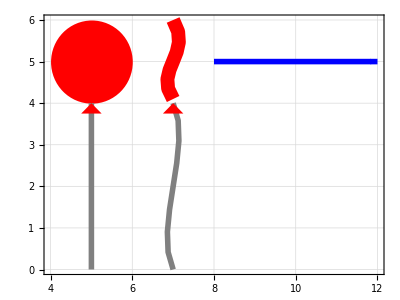

```mathematica
Graphics[{drawBalloon[{5,5}],drawPoppedBalloon[{7,5}],drawArrow[{12,5}]},Frame->True,GridLines->Automatic]
```

Once again, we use Table and ListAnimate to create our animation. An If condition tests whether the arrow has reached the balloon or not. We want this animation to run more quickly than the Stop Light animation, so we set the frames per second to 10.

```mathematica
balloonFrames=Table[Graphics[{LightBlue,Rectangle[{-3,0},{20,10}],If[x<16,drawBalloon[{16,5}],drawPoppedBalloon[{16,5}]],drawArrow[{x,5}]}],{x,20}];
```

```mathematica
ListAnimate[balloonFrames,10]
```

## EuclideanDistance

A more general way to implement collision detection is to measure the EuclideanDistance between the centre points of two objects. If it is less than or equal to the sum of their radii, their edges are touching or overlapping. If either or both of the objects are not circles, we imagine the smallest circle they fit inside. (For objects that are long and thin or have irregular edges, we might have to come up with a more sophisticated algorithm).

Here is an example of two disks that are touching. They both have a radius of 1, so the sum of their radii is 2.

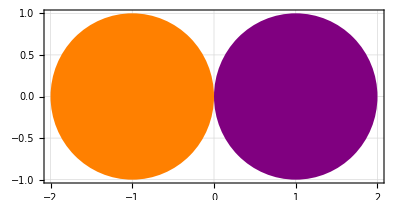

```mathematica
Graphics[{Orange,Disk[{-1,0},1],Purple,Disk[{1,0},1]},Frame->True,GridLines->Automatic]
```

When we measure the EuclideanDistance between the centre points ({-1, 0} and {1, 0}) we find that it is exactly 2, so they are touching.

```mathematica
EuclideanDistance[{-1,0},{1,0}]
```

2

What about a disk of radius 3 centred at {-3, 2} and a disk of radius 2.5 centred at {2, 0.75}? The calculation suggests that they are either touching or overlapping

```mathematica
EuclideanDistance[{-3,2},{2,0.75}]≤(3+2.5)
```

True

When we plot the figure we see that this is true

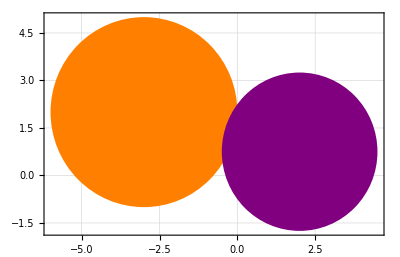

```mathematica
Graphics[{Orange,Disk[{-3,2},3],Purple,Disk[{2,0.75},2.5]},Frame->True,GridLines->Automatic]
```

The Euclidean distance is the length of the line between their two centre points

```mathematica
EuclideanDistance[{-3,2},{2,0.75}]
```

5.15388

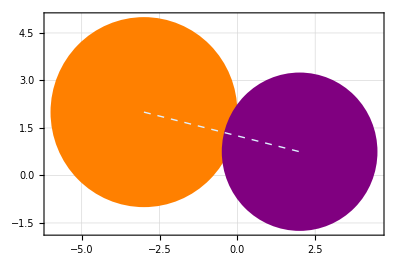

```mathematica
Graphics[{Orange,Disk[{-3,2},3],Purple,Disk[{2,0.75},2.5],LightBlue,Thick,Dashed,Line[{{-3,2},{2,0.75}}]},Frame->True,GridLines->Automatic]
```

## Fireflies

Suppose we want two fireflies to light up when they come near to one another. We can use the EuclideanDistance and an If statement to program this behaviour.

```mathematica
drawFirefly[{x_,y_},lit_]:=
{Lighter[Gray],Disk[{x+1,y},.6],Rotate[Disk[{x,y+1},{.3,1}],45Degree],Thickness[.005],BezierCurve[{{x+1.5,y},{x+.5,y+.5},{x+.8,y+.8},{x+1.5,y+1}}],Disk[{x,y},{1.2,.8}],If[lit,Lighter[Green],Darker[Green]],Disk[{x,y},{1,.6}]}
```

Here is our firefly, unlit and lit

```mathematica
Graphics[{drawFirefly[{5,5},False],drawFirefly[{8,5},True]},Frame->True,GridLines->Automatic]
```

-Graphics-

Now we can use a Manipulate to have one of them fly towards another. When the distance between them drops below a threshold (5 units in this case) they both light up.

```mathematica
Manipulate[Graphics[{Darker[Gray],Rectangle[{-1,0},{22,10}],
If[EuclideanDistance[{13,3},{x,7}]<5,{drawFirefly[{13,3},True],drawFirefly[{x,7},True]},{drawFirefly[{13,3},False],drawFirefly[{x,7},False]}]}],{x,1,20}]
```

## In-Class Activity

### Draw a picture using the Graphics and either the ListAnimate or Manipulate command. Include a conditional statement to dynamically change the behaviour of graphic elements.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course